```mathematica
(* shift +enter to run ;*)
<<Descarta2D`
```

```mathematica
ClearAll[x,y,c,n]
```

Sketch2D::notReal: <25> object(s) cannot be sketched.

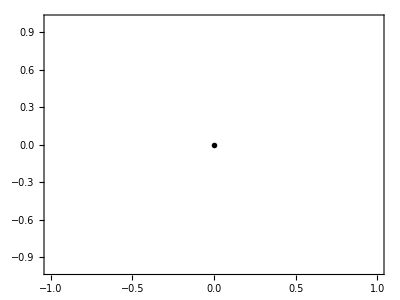

```mathematica
n= Input[StringJoin[ "Alegeti 0 pentru cazul general sau orice alta valoare pentru a seta coordonate arbitrare."]];
(Label[begin];
(*
1. Alegem 3 puncte arbitrare :
A(x,y);
  B(0,0);
  C(c,0);
*)
pA = Point2D[{x, y}];
pB = Point2D[{0, 0}];
pC = Point2D[{c, 0}];
(* 
2. Trasam segmentele delimitate de cele trei puncte si anume : AB,AC,BC
Pentru a forma un triunghiu. 
*)
AB=Segment2D[pA,pB];
AC=Segment2D[pA,pC];
BC= Segment2D[pB,pC];
(*
3. Pentru a determina proiectia lui A pe BC (punctul A1) trasam perpendiculara din A pe BC (reprezentand chiar inaltimea).
*)
AA1= Line2D[pA,Line2D[BC],Perpendicular2D];
pA1 = Point2D[Line2D[BC],AA1] ;
AA1 =Segment2D[pA,pA1];

(*
4'
a) Trasam proiectile (perpendicularele) lui A1 pe AB respectiv pe AC in punctele A2 si A3.
*)
A1A2 = Line2D[pA1,Line2D[AB],Perpendicular2D];
pA2 = Point2D[A1A2,Line2D[AB]];
A1A2 = Segment2D[pA1,pA2];
A1A3 = Line2D[pA1,Line2D[AC],Perpendicular2D]; 
pA3 = Point2D[A1A3,Line2D[AC]]; 
A1A3 = Segment2D[pA1,pA3]; 
(* 
4''.
a) Trasam proiectia lui B pe AC in punctul B2 (a doua inaltime) si proiectile punctului rezultat pe BC respectiv pe AB.
*)
BB1= Line2D [pB , Line2D[AC],Perpendicular2D] ;
pB1= Point2D[BB1,Line2D[AC]]; 
BB1 = Segment2D[pB,pB1] ;
B1B2 = Line2D[pB1 , Line2D[AB],Perpendicular2D]; 
pB2 = Point2D [B1B2 , Line2D[AB]]; 
B1B2 = Segment2D[pB1,pB2]; 
B1B3 = Line2D[pB1,Line2D[BC]] ;
pB3 = Point2D[B1B3,Line2D[BC]]; 
B1B3 = Segment2D[pB1,pB3]; 
(*
b) Trasam proiectia lui C pe AB in punctul C2 (a treia inaltime) si proiectile punctului rezultat pe AC respectiv pe BC.
*)
CC1 = Line2D [pC,Line2D[AB],Perpendicular2D]; 
pC1 = Point2D[CC1,Line2D[AB]]; 
CC1= Segment2D[pC,pC1] ;
C1C2 = Line2D[pC1,Line2D[AC]]; 
pC2 = Point2D[C1C2,Line2D[AC]]; 
C1C2=Segment2D[pC1,pC2]; 
C1C3 = Line2D[pC1,Line2D[BC]] ;
pC3 = Point2D[C1C3,Line2D[BC]]; 
C1C3 = Segment2D[pC1,pC3]; 
(* Fixam ortocentrul triunghiului *)
pO=Point2D[Line2D[AA1],Line2D[BB1]];
(* 
5.
Trasam cercul care trece prin A2, B2 si C2.
*)
CircleABC2=Circle2D[pA2,pB2,pC2];
(* 
6.
Introducem coordonatele lui A si coordonata x a lui C pana cand punctele rezultate formeaza un triunghi.
*)
If[n==3339,Goto[end],n=n];
(Label[first];
If[n==0,Goto[second],n=3339];
(Label[start];
x=Input[StringJoin[ "Da coordonata x a punctului A"]];
y= Input[StringJoin["Da coordonata y a punctului A"]];
c= Input [StringJoin["Da coordonata x a punctului C"]];
dAB = Distance2D[pA,pB];
dAC = Distance2D[pA,pC];
dBC=Distance2D[pB,pC];
If[dAB<dBC+dAC&&dBC<dAB+dAC&&dAC<dAB+dBC,Goto[stop],Goto[start]];
Label[stop]);
Label[second])
If[n==3339,Goto[begin],n=n];
Label[end];)
Sketch2D[{AB,BC,AC,AA1,pA,pB,pC,pA1,pA2,A1A2,pA3,A1A3,pB1,BB1,pB2,B1B2,pB3,B1B3,pC1,CC1,pC2,C1C2,pC3,C1C3,CircleABC2,pO}]
```

```mathematica
{IsOn2D[pA3,CircleABC2],IsOn2D[pB3,CircleABC2],IsOn2D[pC3,CircleABC2]}
```

{True,True,True}